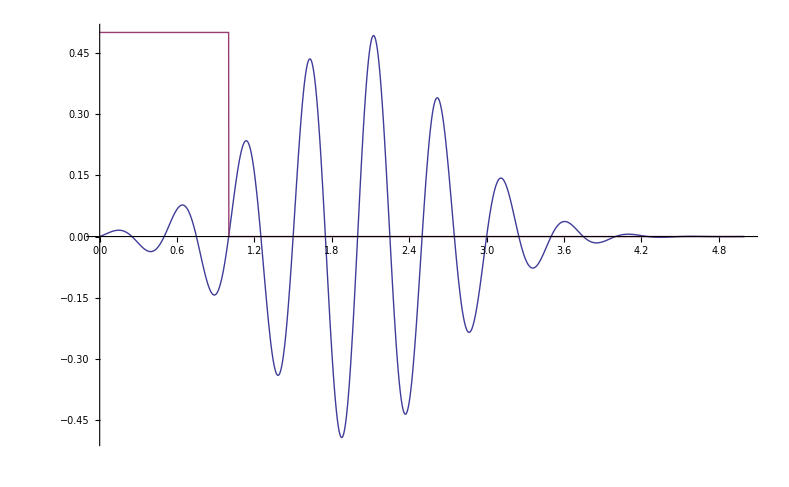

```mathematica
Ef[t_,A_,ω_,t0_,τ_]:=A*Cos[ω*(t-t0)-π/2]*Exp[-((t-t0)^2)/(τ^2)]
Wf[t_,A_,τ_]:=A*HeavisideTheta[τ-Abs[t]]
Plot[{Ef[x,0.5,4π,2,1],Wf[x,0.5,1]},{x,0,5},PlotRange->Full]
```

```mathematica
FullSimplify[Integrate[Ef[t,A,ω,t0,τ],t]]
```

1/4 ⅈ A ⅇ^(-1/4 τ^2 ω^2) √π τ (-Erf[(t-t0)/τ-(ⅈ τ ω)/2]+Erf[(t-t0)/τ+(ⅈ τ ω)/2])